#### REF:”Practical Applications of Bayesian Reliability”

```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
CHAINS=5;
```

```mathematica
successes={59,59,59,59,299,299,299,299,12};sampleSize={59,59,59,59,299,299,299,299,12};
```

```mathematica
qinit=Table[RandomVariate[UniformDistribution[{0,1}],CHAINS],{i,11}]//Transpose;
```

```mathematica
θ={θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8,θ9};
```

```mathematica
outbnd[q_]:=AnyTrue[q[[1;;9]],(#<=0||#>=1)&]||AnyTrue[q[[10;;11]],(#<=0)&];
```

```mathematica
INTERVAL=1001;
STEPS=2;
```

```mathematica
U[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_,θ7_,θ8_,θ9_,α_,β_]=Simplify[PowerExpand[-Log[Simplify[PDF[GammaDistribution[1,1],α],α>0]]]+PowerExpand[-Log[Simplify[PDF[GammaDistribution[1,1],β],β>0]]]+Sum[PowerExpand[-Log[Simplify[PDF[BetaDistribution[α1,β1],th],0<th<1]]-Log[Simplify[PDF[BinomialDistribution[n,p],x],0≤x≤n]]]/.{α1->α+1,β1->β+1,th->θ[[i]],p->θ[[i]],n->sampleSize[[i]],x->successes[[i]]},{i,9}]];
dU[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_,θ7_,θ8_,θ9_,α_,β_]=Simplify[GradientG[U[θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8,θ9,α,β],{θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8,θ9,α,β}]];
ddU[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_,θ7_,θ8_,θ9_,α_,β_]=Simplify[HessianH[U[θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8,θ9,α,β],{θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8,θ9,α,β}]];
```

```mathematica
KU=10;
QS=hmc[U,dU,ddU,11,20000,30000,True,True,qinit];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{108.643,0.,0.,0.,0.,0.,0.,0.,0.,-1.28126,4.5554},«9»,{4.5554,2.9491,2.8626×10^8,1.47746,59.0147,2.44634,1.89627,42.2847,2.37508,-1.03573,13.7687}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{22956.2,0.,0.,0.,0.,0.,0.,0.,0.,-1.00158,634.125},«9»,{634.125,858.676,273.037,1.90506,259.151,29396.3,952.289,6563.24,224.7,-0.422833,13.2388}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{26045.2,0.,0.,0.,0.,0.,0.,0.,0.,-1.00143,702.612},«9»,{702.612,939.071,350.871,1.87952,331.039,31773.9,1043.03,7103.5,344.094,-0.448071,13.2939}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

100185.125629.09160.5039710.47043836.5785121.704183.2910.0003991750.0830145True{1,2}{3}

2002153.374134.4990.4491270.405201250.963270.774404.3370.002017620.0468595False{1,2}{2,3}

3003-287.73732.96470.1273380.158416558.421270.684490.9940.0008556680.0320057True{1,3}{1,3}

4004-110.0321740.180.4801360.49311601.026270.684490.9940.0005844320.0425996False{1,2}{1,3}

5005-335.33328.35610.3964020.432835606.016270.684490.9940.0007071630.0218603True{1,2,3}{1,3}

6006-108.394383.9210.348850.43393599.388270.684490.9940.0005313020.0387269False{1,2}{1,3}

7007-328.87423.59930.2327550.429883599.558270.684490.9940.0006428760.0352063True{1,2,3}{1,3}

8008-81.831563.8690.6947070.40236572.825270.684490.9940.0006428760.0290961False{1,2}{3}

9009-326.131.06730.3396660.46972596.784270.684490.9940.0007071630.0240463True{1}{3}

10010-132.353222.4690.2333730.248582623.347270.684490.9940.0006428760.0320057False{1}{2,3}

11011-309.28327.61050.2620680.164801579.966270.684490.9940.0004390930.0352063True{1,2}{1,3}

12012-101.018209.6940.4285280.522738592.012270.684490.9940.0004830020.0352063False{1,2}{1,3}

13013-292.1326.72010.2581410.41173562.814270.684490.9940.0004390930.0320057True{1,2}{1,3}

14014-95.2064413.2660.313470.180501586.2270.684490.9940.000777880.0352063False{1,2}{1,3}

15015-320.26429.90630.3730070.453644590.948270.684490.9940.0006428760.0425996True{1}{3}

16016-105.258500.2780.5733240.446218596.251270.684490.9940.0005313020.0320057False{1,3}{1,3}

17017-312.99223.11280.3464770.483776583.676270.684490.9940.000777880.0387269True{1,2,3}{1,3}

18018-82.5277507.6680.2612420.217914573.522270.684490.9940.0005844320.0352063False{1}{3}

19019-323.8521.51940.4810710.453293594.534270.684490.9940.0005844320.0387269True{1,2,3}{1,3}

20020-112.562427.5280.3403170.389722603.556270.684490.9940.0004390930.0352063False{1,2}{1,3}

21021-321.26726.4690.3506180.387047591.95270.684490.9940.0004390930.0352063True{1,2}{1,3}

22022-97.4797778.2120.3269850.385622588.474270.684490.9940.0004390930.0352063False{1,2}{1,3}

23023-316.31535.64510.4216260.342105586.998270.684490.9940.0004390930.0352063True{1,2}{1,3}

24024-84.8872179.5440.5607420.413958575.881270.684490.9940.0004390930.0352063False{1,2}{1,3}

25025-337.41320.53320.5211160.36915608.097270.684490.9940.0004390930.0352063True{1,2}{1,3}

26026-114.602236.6530.4176610.531918605.595270.684490.9940.0004390930.0352063False{1,2}{1,3}

27027-328.49736.82140.5124660.445407599.181270.684490.9940.0004390930.0352063True{1,2}{1,3}

28028-116.758346.4870.4052490.384929607.751270.684490.9940.0004390930.0352063False{1,2}{1,3}

29029-311.95419.07630.4476550.335269582.638270.684490.9940.0004390930.0352063True{1,2}{1,3}

```mathematica
QQ=Table[QS[[i;;Length[QS];;CHAINS,;;]],{i,1,CHAINS}];
```

```mathematica
QQ//Dimensions
```

{5,10000,11}

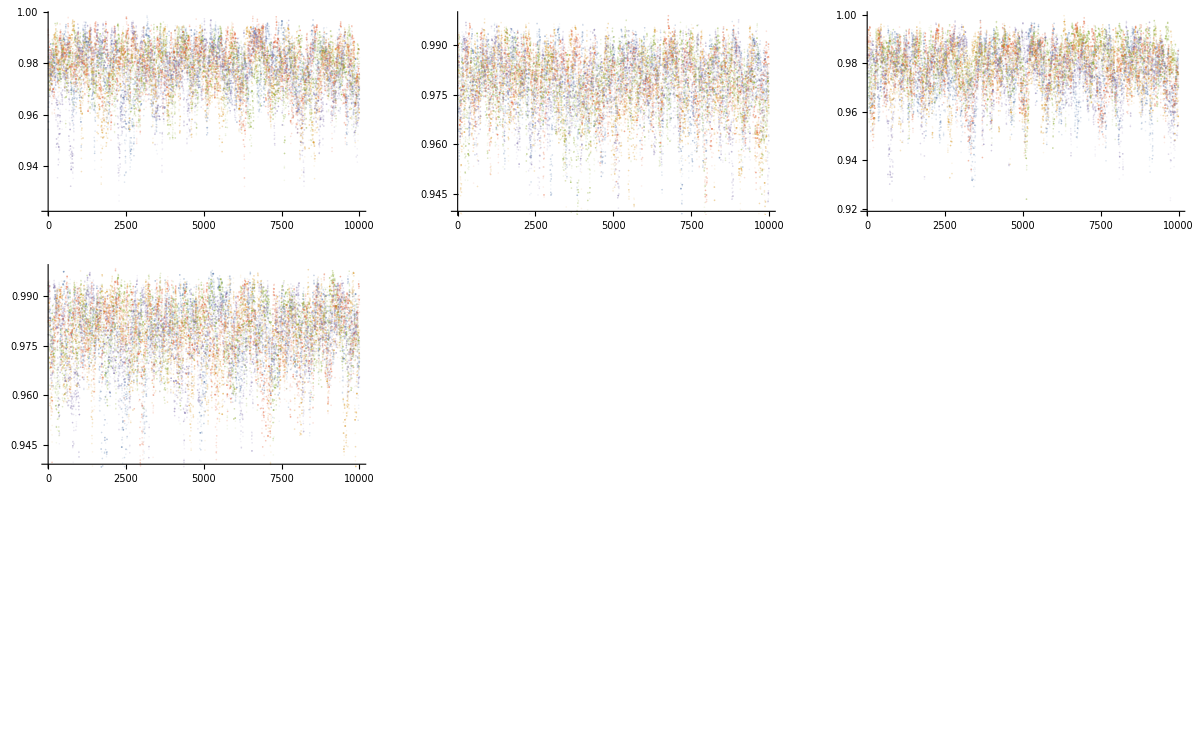

```mathematica
GraphicsGrid[ArrayReshape[Table[ListPlot[Table[QQ[[i,;;,j]],{i,CHAINS}],(*Ticks->{None,None}*)PlotStyle->Opacity[.1]],{j,9}],{3,3}]]
```

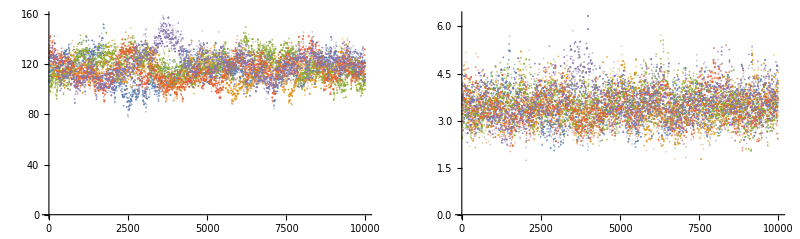

```mathematica
GraphicsRow[Table[ListPlot[Table[QQ[[i,;;,j]],{i,CHAINS}],PlotStyle->Opacity[.3](*,Ticks->None*)],{j,10,11}]]
```

```mathematica
theta9=Import["/var/u1/Downloads/Computer_scripts_and_data_files/theta9_samples.csv"];
theta1=Import["/var/u1/Downloads/Computer_scripts_and_data_files/theta1_samples.csv"];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

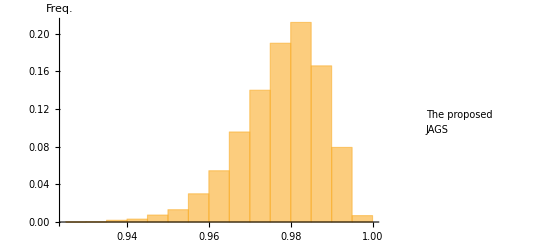

```mathematica
Histogram[{QS[[;;,1]],theta1[[;;,2]]},Automatic,"Probability",ChartStyle->{Opacity[.6],Ticks->None,Opacity[.1]},AxesLabel->{None,"Freq."},ChartLegends->Placed[{"The proposed","JAGS"},Center]]
```

```mathematica
theta10//Dimensions
```

{50000}

```mathematica
QS//Dimensions
```

{50000,11}

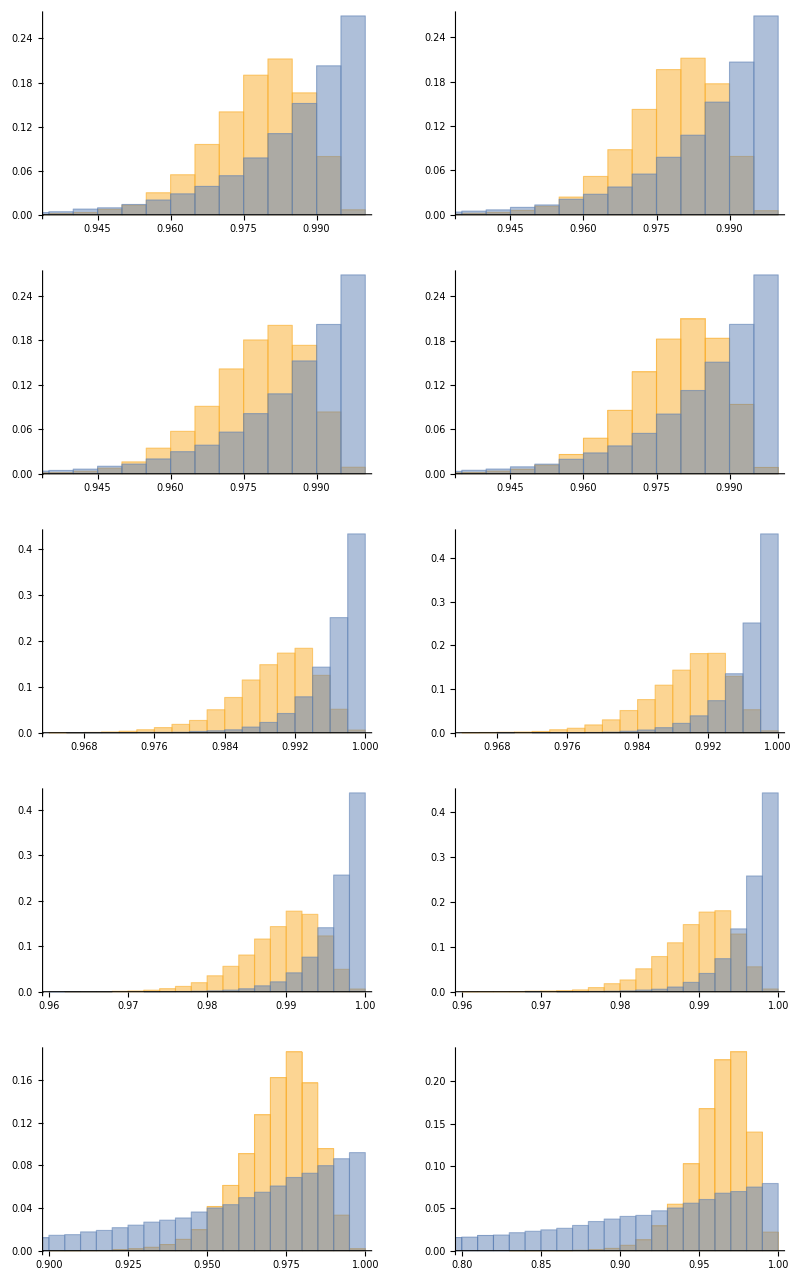

```mathematica
GraphicsGrid[ArrayReshape[Table[Histogram[{If[j<10,QS[[;;,j]],theta10],thetas[[;;,j]]},Automatic,"Probability",ChartLabels->{None,j}],{j,1,10}],{5,2}]]
```

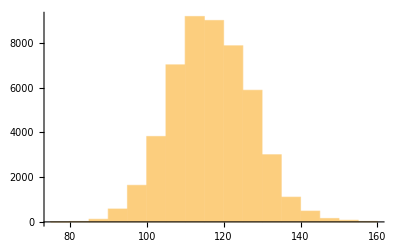

```mathematica
Histogram[QS[[;;,10]]]
```

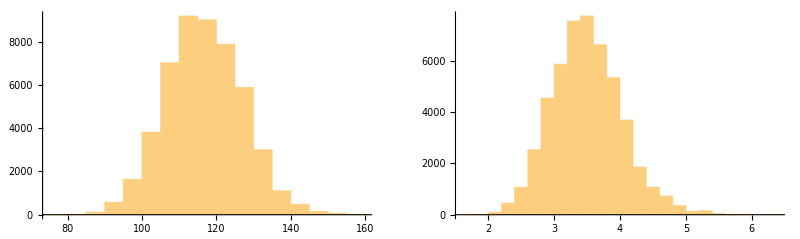

```mathematica
GraphicsRow[Table[Histogram[QS[[;;,j]]],{j,10,11}]]
```

```mathematica
psrf1=psrf[QS];
```

```mathematica
psrf1
```

{1.01319,1.00256,1.02964,1.00783,1.00206,1.00178,1.00278,1.00411,1.00595,1.04429,1.01825}

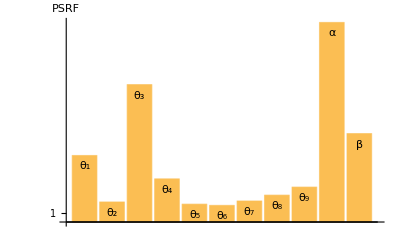

```mathematica
BarChart[psrf1,ChartLabels->Placed[{"θ_1","θ_2","θ_3","θ_4","θ_5","θ_6","θ_7","θ_8","θ_9","α","β"},Top],PlotRange->{Automatic,{.998,Max[psrf1]}},AxesLabel->{None,"PSRF"},ScalingFunctions->"Log"]
```

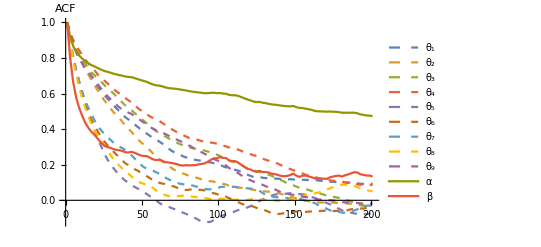

```mathematica
ListPlot[Table[CorrelationFunction[QQ[[1,;;,i]],{200}],{i,11}],(*Filling->Axis,*)PlotRange->All,PlotStyle->{Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashing,Dashing},Joined->True,AxesLabel->{None,"ACF"},PlotLegends->{"θ_1","θ_2","θ_3","θ_4","θ_5","θ_6","θ_7","θ_8","θ_9","α","β"}]
```

```mathematica
theta10=Table[RandomVariate[BetaDistribution[QS[[i,10]]+1,QS[[i,11]]+1]],{i,Length[QS]}];
```

```mathematica
Quantile[theta10,{0.025,0.5,0.975}]//MatrixForm
```

(0.920623
0.965746
0.989532)

```mathematica
StandardDeviation[theta10]
```

0.0178858

```mathematica
{StandardDeviation[QS]}//Transpose//MatrixForm
```

(0.00999381
0.00978878
0.0104411
0.0102175
0.00479928
0.0048324
0.00491322
0.00475789
0.0117747
10.2536
0.528799)

```mathematica
StandardDeviation[QS]
```

{0.00999381,0.00978878,0.0104411,0.0102175,0.00479928,0.0048324,0.00491322,0.00475789,0.0117747,10.2536,0.528799}

```mathematica
StandardDeviation[theta10]
```

0.0179723

```mathematica
Quantile[QS,{0.025,0.5,0.975}]//MatrixForm
```

(0.954865 | 0.979083 | 0.993165
0.955474 | 0.979403 | 0.99293
0.953751 | 0.979091 | 0.993441
0.954892 | 0.979855 | 0.99346
0.978151 | 0.990464 | 0.996855
0.978202 | 0.990588 | 0.996911
0.977997 | 0.990266 | 0.996924
0.978762 | 0.990549 | 0.997037
0.945639 | 0.974276 | 0.990805
97.1468 | 116.426 | 136.782
2.55776 | 3.47036 | 4.6529)

```mathematica
codaMatrix
```

{{alpha,beta,theta[10],theta[1],theta[2],theta[3],theta[4],theta[5],theta[6],theta[7],theta[8],theta[9]},{10.2287,0.0390528,0.989974,0.997299,0.983261,0.985654,0.992858,0.998634,0.993508,0.997567,0.999689,0.978872},29998,{19.6917,0.103501,0.856037,0.992455,0.979124,0.999854,0.974015,0.999379,0.998081,0.99795,0.999104,0.987968}}
 |  |  |  |

```mathematica
Mean[codaMatrix[[2;;,;;]]]
```

{8.20758,0.0418044,0.889943,0.984933,0.985049,0.9849,0.984944,0.996555,0.996754,0.996622,0.996695,0.952628}

```mathematica
Quantile[theta10,{0.025,0.05,0.5,0.95,0.975}]
```

{0.920321,0.929495,0.965921,0.987003,0.989597}

```mathematica
Export["hier_binomial.csv",QS]
```

hier_binomial.csv

```mathematica
(*QS=Import["hier_binomial.csv"];*)
```

```mathematica
QS=Import["hier_binomial.csv"];
```

```mathematica
codaMatrix=Import["/var/u1/Downloads/Computer_scripts_and_data_files/codaMatrix.csv"];
```

```mathematica
codaMatrix
```

{{alpha,beta,theta[10],theta[1],theta[2],theta[3],theta[4],theta[5],theta[6],theta[7],theta[8],theta[9]},{10.2287,0.0390528,0.989974,0.997299,0.983261,0.985654,0.992858,0.998634,0.993508,0.997567,0.999689,0.978872},29998,{19.6917,0.103501,0.856037,0.992455,0.979124,0.999854,0.974015,0.999379,0.998081,0.99795,0.999104,0.987968}}
 |  |  |  |

```mathematica
thetas=codaMatrix[[2;;,{4,5,6,7,8,9,10,11,12,3}]]
```

{{0.997299,0.983261,0.985654,0.992858,0.998634,0.993508,0.997567,0.999689,0.978872,0.989974},{0.996091,0.98596,0.996508,0.999786,0.996886,0.990651,0.998559,0.999955,0.973913,0.913056},29996,{0.989557,0.997335,0.963794,0.959076,0.999788,0.999556,0.994865,0.998779,0.99985,0.987029},{0.992455,0.979124,0.999854,0.974015,0.999379,0.998081,0.99795,0.999104,0.987968,0.856037}}
 |  |  |  |

```mathematica
ab=codaMatrix[[2;;,{1,2}]]
```

{{10.2287,0.0390528},{15.2879,0.0673867},{2.68769,0.0429148},{1.7423,0.0275841},{13.8621,0.0356236},{10.0361,0.00793553},{5.3836,0.0121248},{5.97566,0.00489327},{6.2596,0.0483979},{5.93025,0.0373955},29981,{9.043,0.168231},{6.11338,0.0866556},{8.64532,0.0134313},{7.12706,0.00702734},{7.33653,0.0127403},{10.2174,0.0160124},{9.89377,0.0522187},{15.062,0.073287},{19.6917,0.103501}}
 |  |  |  |